```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];

Import["model/data.wl"];
Import["model/plot-utils.wl"];
Import["model/model.wl"];
```

```mathematica
state="CA";

params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
icuCapacity=params["icuBeds"]/params["population"];
thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
hospitalCapacity=(1-params["bedUtilization"])params["staffedBeds"]/params["population"];
hospitalizationData = stateHospitalizationData[state];
```

```mathematica
distance[t_] := stateDistancing[state,scenario1,t];
sol=CovidModelFit[
daysUntilNotInfectiousOrHospitalized0,
daysFromInfectedToInfectious0,
daysUntilNotInfectiousOrHospitalized0,
daysToLeaveHosptialNonCritical0,
pPCRNH0,
pPCRH0,
daysTogoToCriticalCare0,
daysFromCriticalToRecoveredOrDeceased0,
fractionOfCriticalDeceased0,
importlength0,initialInfectionImpulse0,
tmax,
params["pS"],
params["pH"],
params["pC"],
distance,
icuCapacity
]
model[r0natural_,importtime_][i_,t_]:=Through[sol[r0natural,importtime][t],List][[i]]/;And@@NumericQ/@{r0natural,importtime,i,t}
```

ParametricFunction[<>]

```mathematica
longData=Select[Join[{1,#["day"],If[TrueQ[#["deathIncrease"]==Null],0,(#["deathIncrease"]/params["population"])//N]}&/@thisStateData,
{2,#["day"],(#["positiveIncrease"]/params["population"])//N}&/@thisStateData
],#[[3]]>0&];
```

{{1,90.,5.13046×10^-7},{1,89.,2.56523×10^-7},{1,88.,5.64351×10^-7},{1,87.,5.90003×10^-7},{1,86.,3.3348×10^-7},{1,85.,3.07828×10^-7},{1,84.,3.3348×10^-7},{1,83.,3.3348×10^-7},{1,81.,7.69569×10^-8},{1,80.,1.02609×10^-7},{1,79.,5.13046×10^-8},{1,78.,1.28262×10^-7},{1,77.,5.13046×10^-8},{1,76.,1.28262×10^-7},{1,75.,2.56523×10^-8},{1,73.,2.56523×10^-8},{1,71.,1.02609×10^-7},{2,90.,0.0000265501},{2,89.,0.0000189571},{2,88.,0.0000273197},{2,87.,0.0000195984},{2,86.,0.0000223945},{2,85.,0.0000166997},{2,84.,6.49003×10^-6},{2,83.,9.4657×10^-6},{2,82.,5.0535×10^-6},{2,81.,6.59264×10^-6},{2,80.,5.5409×10^-6},{2,79.,3.56567×10^-6},{2,78.,8.02917×10^-6},{2,77.,3.2835×10^-6},{2,76.,3.79654×10^-6},{2,75.,1.0774×10^-6},{2,74.,1.05174×10^-6},{2,73.,1.28262×10^-6},{2,71.,1.15435×10^-6},{2,70.,6.15655×10^-7},{2,69.,4.87394×10^-7},{2,68.,6.6696×10^-7},{2,67.,4.87394×10^-7},{2,66.,2.30871×10^-7},{2,65.,1.79566×10^-7}}

{0.0455,0.091,0.0413636,0.0395652,0.07,0.0758333,0.07,0.07,0.303333,0.2275,0.455,0.182,0.455,0.182,0.91,0.91,0.2275,0.000800097,0.00112057,0.000777559,0.0010839,0.000948568,0.00127204,0.00327312,0.00224417,0.00420355,0.00322218,0.0038338,0.00595755,0.00264569,0.00646953,0.00559527,0.0197167,0.0201976,0.016562,0.0184022,0.0345042,0.0435842,0.03185,0.0435842,0.0920111,0.1183}

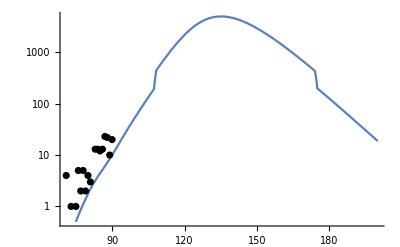

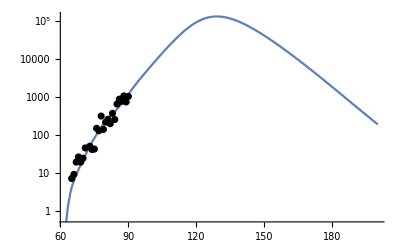

```mathematica
dataWeights=(.91^#[[1]](params["population"]#[[3]])^-1)&/@longData
fit=NonlinearModelFit[
longData,
model[r0natural,importtime][i,t] - model[r0natural,importtime][i,t-1],
{{r0natural, Log[r0natural0]}, {importtime, Log[params["importtime0"]]}},
{i,t},
Weights -> dataWeights,
AccuracyGoal->5,
PrecisionGoal->10
];
Show[
LogPlot[{params["population"]fit[1,t]},{t,60,200},PlotRange->{Automatic,{.5,All}}],
ListLogPlot[{
{#["day"],#["deathIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
Show[
LogPlot[{params["population"]fit[2,t]},{t,60,200},PlotRange->{Automatic,{.5,All}}],
ListLogPlot[{
{#["day"],#["positiveIncrease"]}&/@thisStateData
},PlotStyle->Black]
]
```

```mathematica
ApplylongData[[All,1]]==1
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}==1

```mathematica
gofMetrics=goodnessOfFitMetrics[fit["FitResiduals"],longData]
```

<|chiSquared→4.54668×10^-7,rmsRelativeError→0.507573,rmsRelativeErrorDeaths→0.63943,rmsRelativeErrorPcr→0.39343,meanRelativeErrorDeaths→0.605468,meanRelativeErrorPCR→0.0210459,rSquaredDeaths→1.09282,rSquaredPCR→0.124271|>

```mathematica
columnOrder={"chiSquared",
		"rmsRelativeError",
		"rmsRelativeErrorDeaths",
		"rmsRelativeErrorPcr",
		"meanRelativeErrorDeaths",
		"meanRelativeErrorPCR",
		"rSquaredDeaths",
		"rSquaredPCR"};gofAssociationToArray[gofMetrics_]:=Map[gofMetrics[#]&,columnOrder];
gofAssociationToArray[gofMetrics]
```

{4.54668×10^-7,0.507573,0.63943,0.39343,0.605468,0.0210459,1.09282,0.124271}

{{1,AK,0.60.6,0.00.4,Null},{2,CA,0.60.6,0.00.4,Null},{3,NV,0.60.6,0.00.4,Null}}

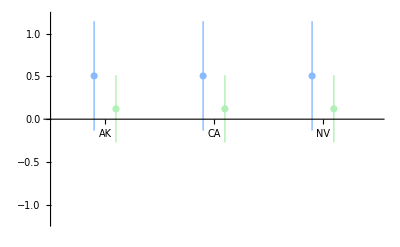

Show

```mathematica
allStateData=<|
"CA"-><|
"goodnessOfFitMetrics"-><|"chiSquared"->4.546683324965723*^-7,"rmsRelativeError"->0.5075731819678969,"rmsRelativeErrorDeaths"->0.6394299646210302,"rmsRelativeErrorPcr"->0.3934300912786099,"meanRelativeErrorDeaths"->0.6054675506474274,"meanRelativeErrorPcr"->0.021045925499913434,"rSquaredDeaths"->1.092816520387405,"rSquaredPcr"->0.12427052021763794|>
|>,
"NV"-><|
"goodnessOfFitMetrics"-><|"chiSquared"->4.546683324965723*^-7,"rmsRelativeError"->0.5075731819678969,"rmsRelativeErrorDeaths"->0.6394299646210302,"rmsRelativeErrorPcr"->0.3934300912786099,"meanRelativeErrorDeaths"->0.6054675506474274,"meanRelativeErrorPcr"->0.021045925499913434,"rSquaredDeaths"->1.092816520387405,"rSquaredPcr"->0.12427052021763794|>
|>,
"AK"-><|
"goodnessOfFitMetrics"-><|"chiSquared"->4.546683324965723*^-7,"rmsRelativeError"->0.5075731819678969,"rmsRelativeErrorDeaths"->0.6394299646210302,"rmsRelativeErrorPcr"->0.3934300912786099,"meanRelativeErrorDeaths"->0.6054675506474274,"meanRelativeErrorPcr"->0.021045925499913434,"rSquaredDeaths"->1.092816520387405,"rSquaredPcr"->0.12427052021763794|>
|>
|>;
data=MapIndexed[
Join[#2,#1]&,
Sort[KeyValueMap[{
#1,
Around[
#2["goodnessOfFitMetrics"]["meanRelativeErrorDeaths"],
#2["goodnessOfFitMetrics"]["rmsRelativeErrorDeaths"]],
Around[
#2["goodnessOfFitMetrics"]["meanRelativeErrorPcr"],
#2["goodnessOfFitMetrics"]["rmsRelativeErrorPcr"]],

}&,allStateData]]]
Show[
ListPlot[data[[All,{1,3}]]-.1,Ticks->{data[[All,{1,2}]],Automatic},PlotRange->{{.5,Length[data]+.5},{-1.2,1.2}},PlotStyle->{RGBColor["#88bbfe"]}],
ListPlot[data[[All,{1,4}]]+.1,PlotStyle->{RGBColor["#aff1b6"]}]
]
Show
```

```mathematica
AlphabeticOrder["CA","WA"]
```

1

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"];
```

```mathematica
GenerateModelExport[20,{"CA"}]
```

generating data for CA

```mathematica
evaluateState["CA", 20]
```

```mathematica
(*fit R0/import time per state,then forecast each scenario*)

state="CA"
    (* fit R0 / import time per state, then forecast each scenario *)
    params=stateParams[state,pC0,pH0,medianHospitalizationAge0,ageCriticalDependence0,ageHospitalizedDependence0];
	icuCapacity=params["icuBeds"]/params["population"];
	thisStateData=Select[parsedData,(#["state"]==state&&#["positive"]>0)&];
	hospitalCapacity=(1-params["bedUtilization"])*params["staffedBeds"]/params["population"];
	hospitalizationData = stateHospitalizationData[state];
	
    (* just do the fit to scenario1, the fit happens on points that are in the past, sot he future scenario doesn't impact *)
	setDistancing[state,scenario1];
	
	sol=CovidModelFit[
	daysUntilNotInfectiousOrHospitalized0,
	daysFromInfectedToInfectious0,
	daysUntilNotInfectiousOrHospitalized0,
	daysToLeaveHosptialNonCritical0,
	pPCRNH0,
	pPCRH0,
	daysTogoToCriticalCare0,
	daysFromCriticalToRecoveredOrDeceased0,
	fractionOfCriticalDeceased0,
	importlength0,
	initialInfectionImpulse0,
	tmax0,
	params["pS"],
	params["pH"],
	params["pC"],
	distancing,
	icuCapacity
	];

    model[r0natural_,importtime_][i_,t_]:=Through[sol[r0natural,importtime][t],List][[i]]/;And@@NumericQ/@{r0natural,importtime,i,t};
	
	(* we make the data shape (metric#, day, value) so that we can simultaneously fit PCR and deaths *)
	longData=Select[Join[
	  {1,#["day"],If[TrueQ[#["deathIncrease"]==Null],0,(#["deathIncrease"]/params["population"])//N]}&/@thisStateData,
	  {2,#["day"],(#["positiveIncrease"]/params["population"])//N}&/@thisStateData
	],#[[3]]>0&];
	
	(* set weights for each datapoint in longData *)
	(* apply a week over week weight reduction, i.e. 0.75 indicates that a data point at day 0 is weighted 75% as strongly as a data point at day 7. *)
	(* assume each datapoint otherwise has a constant relative variance (Poissan) for both death and PCR rates. *)
	(* the constant factor of the population shouldn't matter, but the fit chokes if the weights are too small *)
	weekOverWeekWeight=.75;
	dataWeights=(weekOverWeekWeight^(#[[1]]/7)(params["population"]#[[3]])^-1)&/@longData;
	dataWeights=(1)&/@longData;

	(* Switch to nminimize, if we run into issues with the multi-fit not respecting weights *)
	(* confidence interval we get from doing the log needs to be back-transformed *)
	(* unclear how easy it is to get parameter confidence intervals from nminmize *)
	fit=NonlinearModelFit[
		longData,
		(* fit to daily increases *) 
		(* TODO log the model and log the data *)
		model[r0natural,importtime][i,t] - model[r0natural,importtime][i,t-1], 
		{{r0natural, Log[r0natural0]}, {importtime, Log[params["importtime0"]]}},
		{i,t},
		Weights -> dataWeights,
		AccuracyGoal->5,
		PrecisionGoal->10
	];
```

CA

ParametricNDSolveValue::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

General::stop: Further output of ParametricNDSolveValue::icfail will be suppressed during this calculation.

Part::partw: Part 2. of ParametricFunction[1,Internal`Bag[<1>],0,1,{{r0natural$1356917,importtime$1356918},«4»,{Automatic,0,0}},{NDSolve`base$1356957,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolveValue,Internal`Bag[<2>],None,ParametricNDSolveValue},«6»,{},All]}][«1»][90.] does not exist.

Part::partw: Part 2. of ParametricFunction[1,Internal`Bag[<1>],0,1,{{r0natural$1356917,importtime$1356918},«4»,{Automatic,0,0}},{NDSolve`base$1356957,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolveValue,Internal`Bag[<2>],None,ParametricNDSolveValue},«6»,{},All]}][«1»][91.] does not exist.

Part::partw: Part 2. of ParametricFunction[1,Internal`Bag[<1>],0,1,{{r0natural$1356917,importtime$1356918},«4»,{Automatic,0,0}},{NDSolve`base$1356957,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolveValue,Internal`Bag[<2>],None,ParametricNDSolveValue},«6»,{},All]}][«1»][89.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {1.,«19»,«40»,«1»,1. (-1.79566×10^-7-1. «1»+ParametricFunction[1,Internal`Bag[<1>],«3»,{NDSolve`base$1356957,NDSolve`NDSolveParametricFunction[0,{«4»},{«4»},{«17»},{«5»},{«1»},{«27»},{«7»},{},All]}][1.1314,4.02535][65.]⟦2.⟧)} is not a list of real numbers with dimensions {44} at {r0natural,importtime} = {1.1314,4.02535}.